## Mathematica Tips and Tricks:

Mathematica has extensive help online. The Mathematica Documentation Center will be an important source of information for you as you go through the class. Refer to it often.

The syntax in Mathematica can be confusing at first. There are a lot of shortcuts and tools you can use to make tasks easier. For example, you can introduce symbols that are not on the keyboard by using “escape”. To get the Greek letter δ (delta), for example, you can press the escape button, then the letter d, then the escape button again, <esc> <d> <esc>. If you want the capital delta, Δ, just type <esc> <D> <esc>. This applies to most Greek letters, and a lot of them correspond to the letters in the English alphabet that you would imagine (“α” corresponds to “a”,“β” to “b”, etc...). To learn all of the shortcuts or to see all that is available to you, click on the “Palettes” tab on the menu bar and open the “Classroom Assistant” palette. This palette gives you the ability to click on a symbol, function or calculation... and enter it into your notebook. To change the input format, from input code to simply text for example, click on the “Format” menu and go to the “Style” menu. This will allow you to change the input style for any cell. It will also give you the keyboard shortcuts for each type of style. For example, the shortcut for Text is <Alt>+<7> and the shortcut for a title is <Alt>+<1>. 

Sometimes adding comments to your input cells can be helpful for specifying what the input means or displaying the units without printing it in the output. This can be done by placing text inside “(*” and closing it with “*)”.

```mathematica
δm=100*2/4.2/Sin[0.5]  (*The text here will turn gray and will not show up inthe output after hitting shift enter*)
```

99.3252

To display an output in scientific notation you can use the command: ScientificForm. For example:

```mathematica
ScientificForm[δm,3]
```

9.93×10^1

However, oftentimes it is more convenient (and sometimes more useful) when working with very large (or very small) numbers to end a line with "//N" instead:

```mathematica
54!
54!//N
```

230843697339241380472092742683027581083278564571807941132288000000000000

2.30844×10^71

Sometimes when you are working, you make errors and have to go back to change things. While doing this, you can accidentally define a specific variable as something and forget that you did. This will cause problems with all later functions involving that variable. If you are running into problems with a function, it can be helpful to clear all prior definitions of the variable using the “Clear” function.

```mathematica
?Clear
```

If you are having a lot of trouble evaluating a particular expression and you have multiple notebooks open and running, then you may have a variable double named. The Clear command typically works to resolve this, however if it does not, you can quit and start the Mathematica kernel (the thinking part of Mathematica) without having to close your document. Under the “Evaluation” tab in the menu go to the bottom where it says “Quit Kernel” then press “Local”. It may take a moment for the kernel to quit, but once it has, go back to the “Evaluation” tab and select “Start Kernel” then press “Local”. The more likely scenario where you will have to use this method is if you have made a mistake in your code, or have a very long algebraic expression, complicated number crunching, etc... and Mathematica has to “think” too long.

## Snappy Tables:

Here are a couple ways to make snappy data tables with column headers, a title, and framing.

For X and Y data in separate lists, you can use the code below. This is useful if you if you have to convert a single column of data to different units, or multiply by a constant, etc...

```mathematica
(*Add your data and labels here*)
xdata={};(*List of Measured Values*)
ydata={};(*List of Measured Values *)
datatitle={{Text["Your Title"],SpanFromLeft}};
datalabel={{"X Label","Y label"}};

(*No need to change the following code!*)
xydata=Thread[{xdata,ydata}]; (*This forms x,y pairs*)
xytable=Join[datatitle,datalabel,xydata];(*This joins the label to the data*)
Grid[xytable,Frame->All] (*The output is  a table and simple plot (optional)*)
ListPlot[xydata]
```

```mathematica
{{□, □}}
```

X and Y data in a single array / matrix. To get a row of an array press:  <Ctrl>+<,>  and to get a column of an array press <Ctrl>+<Enter>. The matrix brackets are gotten from the “Classroom Assistant” under “Basic Commands.” This makes it a bit easier to enter data and proof read it initially. This is best for long sets of data and those that require no conversion, etc...

```mathematica
(*Add your data and labels here*)
```

```mathematica
xyarray=({{□, □}, {□, □}, {□, □}, {□, □}, {□, □}});(*Enter your data in the cells*)
datatitle={{Text["Your Title"],SpanFromLeft}};
datalabel={{"X Label","Y label"}};

(*No need to change the following code!*)
xytable=Join[datatitle,datalabel,xyarray];(*This joins the label to the data*)
Grid[xytable,Frame->All](*The output is a table and simple plot (optional)*)
ListPlot[xytable]
```

In both cases the ListPlot[] is not needed, but gives a quick check to see if the data meets expectation. If you wish, you can give the ListPlot labels, and a name so that later it can be used to plot against a fit or theoretical curve.

One can also form tables using the Prepend[] command rather than joining separate arrays using the Join[] command. These are equivalent methods and depend on the users style and preference. Using the same xydata from before:

```mathematica
Grid[Prepend[Prepend[xyarray,{"X Label","Y Label"}],{"Table Title"}],Frame->All]
```

The Prepend[] command is best used when you only need to quickly add headers to the columns of a data set. If you do not wish to have the table title, one of the Prepend[] commands can be omitted.

```mathematica
Grid[Prepend[xyarray,{"X Label","Y Label"}],Frame->All]
```

One final note on working with lists- occasionally when you need to do several operations one a list, Mathematica will end up redefining your list in vector form (vectors and their notation are described below). For example:

```mathematica
L1={1,2,3,4,5}
L2={6,7,8,9,10}
```

{1,2,3,4,5}

{6,7,8,9,10}

```mathematica
L3={L1[[1;;3]]+L2[[3;;5]],0}
```

{{9,11,13},0}

To fix your list for use in tables or future calculations, use the Flatten[] function:

```mathematica
Flatten[L3]
```

{9,11,13,0}

## Series Expansions:

Often times in physics series expansions of functions are very useful. Mathematica has a built-in function to create power series for combinations of rational functions and transcendental functions, for example:

```mathematica
Series[E^x,{x,0,10}]
Series[x*Sin[x]^2,{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

x^3-x^5/3+O[x]^6

The syntax of the input is the function you want to expand, followed by the variable of interest, the point that's being expanded around, and the number of terms. The "O[x]^11" in the output simply means all terms of order x^11 and higher.

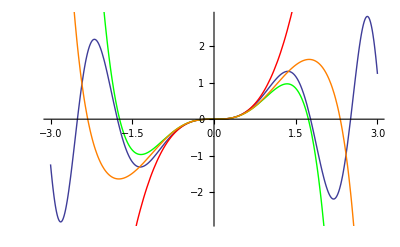

```mathematica
p1=Plot[x*Sin[x^2],{x,-3,3}];
p2=Plot[Evaluate[Normal[Series[x*Sin[x]^2,{x,0,3}]]],{x,-3,3},PlotStyle->Red];
p3=Plot[Evaluate[Normal[Series[x*Sin[x]^2,{x,0,5}]]],{x,-3,3},PlotStyle->Green];
p4=Plot[Evaluate[Normal[Series[x*Sin[x]^2,{x,0,9}]]],{x,-3,3},PlotStyle->Orange];
Show[p1,p2,p3,p4]
```

Increasing the number of terms in the series creates a better fit to the target function. The Normal[] function turns the series expansion into a normal expression (that is, it omits the O[x]^n terms), and the Evaluate[] function lets Mathematica evaluate the resulting expression as a function of x.

## Solving Equations:

Mathematica has many different commands to solve equations, both algebraic and differential. There are two different styles in solving equations: analytically and numerically. If the equation is complicated, then we ought to use the numeric methods to get a useful result.

The most common command to solve algebraic equations is Solve[]. The syntax using this command looks like: Solve[expr,vars]

```mathematica
Solve[x^2+x-8==0,x]
```

{{x→1/2 (-1-√33)},{x→1/2 (-1+√33)}}

Since we solved a quadratic equation we have two solutions. If you want to get a decimal number add the usual //N command at the end of the Solve[] expression.

```mathematica
Solve[x^2+x-8==0,x]//N
```

{{x→-3.37228},{x→2.37228}}

You can also solve equations numerically using the FindRoot[] command. This is useful for complicated equations and when Solve[] yields an useful result. The additional parameter with this command is a guess for a value: FindRoot[f,{x,x_0}]

```mathematica
FindRoot[2-E^(-x),{x,-1}]
```

{x→-0.693147}

Notice that the guess was not spot on, but Mathematica was able to get a numeric value. Mathematically the FindRoot[] function works like Newtons Method.

You can also use Mathematica to solve differential equations, both ordinary and partial, however we will only look at solving ordinary differential equations. We do this using the DSolve[] command. Notice that we include the equation (with double equal signs), the sought for function, and the independent variable: DSolve[eqn,y,x]

```mathematica
DSolve[x''[t]==-k^2*x[t],x[t],t]
```

{{x[t]→C[1] Cos[k t]+C[2] Sin[k t]}}

We can solve the same equation and include some initial conditions. We place them in curly brackets with the equation being solved:

```mathematica
DSolve[{x''[t]==-k^2*x[t],x[0]==1,x'[0]==1},x[t],t]
```

{{x[t]→(k Cos[k t]+Sin[k t])/k}}

Differential equation can be solved numerically in Mathematica. the NDSolve[] command is useful for equations that are nonlinear, coupled, of high order, or a combination of these. The the output of the solution is not an equation as in the previous example, rather Mathematica generates an “Interpolating Function” that we can plot or evaluate at a particular point: NDSolve[eqns,y,{x,x_min,x_max}]

{0.223908}

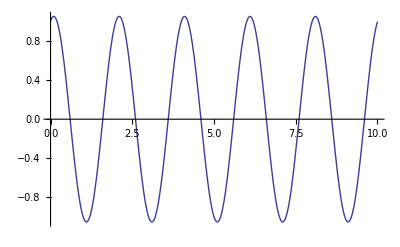

```mathematica
k=3.14;
soln=NDSolve[{x''[t]==-k^2*x[t],x[0]==1,x'[0]==1},x,{t,0,10}];
Evaluate[x[4.532]/.soln]
Plot[Evaluate[x[t]/.soln],{t,0,10},PlotRange-> All]
```

Notice that when we use NDSolve we must specify any parameter, like k, with a particular number. When using the NDSolve[] we must assign it a name so we can use the Evaluate[] command. In this case, the syntax for evaluate is: Evaluate[x[t]/.soln]. Note the “/.soln” which tells Mathematica what it needs to evaluate. The use of the Plot[] command is the same as in the primer, but we use the Evaluate[] command to generate an interpolating function.

(A note on the theory: NDSolve[] is a numerical tool so we can’t get a closed form solution. NDSolve[] typically uses complicated algorithm like Rung-Kutta or Dormand-Prince methods to generate the interpolating function. In most applications these methods are sufficent to produce an approximation with high degree accuracy to the solution.)

## Linear Algebra:

When working with lists and tables of data, often times they are defined as vectors or matrices and can be manipulated as such using linear algebra. 
To start, Mathematica handles matrices in a couple different ways. They can be made using the "Classroom Assistant" Palette, like so:

```mathematica
A1=({{1, 2}, {-2, 4}});
```

Or by using curly braces where the inner braces represent rows, and columns are separated by commas:

```mathematica
A2={{1,2},{-2,4}};
```

You can check that A1 is just a fancier way to show what Mathematica defines the same way as A2.

```mathematica
A1
```

{{1,2},{-2,4}}

If you ever have a matrix or vector in braces but wish to see what it looks like visually, you can add //MatrixForm to the end of the expression to change the output. Note, however, that this causes the output to become a visual graphic (and no longer a geometric entity) so that if you define some vector or matrix with a //MatrixForm at the end, it will NOT produce the desired results when treated as a matrix or vector.

```mathematica
A2//MatrixForm
```

(1 | 2
-2 | 4)

If you wish to make a row vector or a column vector, you can define them similarly to matrices:

```mathematica
V1={{1,2,3}};
V2={{1},{2},{3}};
V1//MatrixForm
V2//MatrixForm
```

(1 | 2 | 3)

(1
2
3)

It should be noted that Mathematica still treats these as matrices, as there are two "sets" of curly braces, those for the rows and those for the columns. Mathematica defines vectors as simply containing one set of braces:

```mathematica
Vector={4,5,4}
```

{4,5,4}

Typing a bunch of curly braces can be a pain for column vectors, so you can use the Transpose[] function (or by simply writing ᵀ after a vector, created by <esc><tr><esc>) on a row vector.

```mathematica
V3=V1ᵀ
```

{{1},{2},{3}}

Which is the same as V2 defined above. Recall that the transpose of a matrix A_ij is A_ij ᵀ=A_ji.

Now for some operations! The dot product in Mathematica is denoted by a period.

```mathematica
V1.V2
Vector.Vector
```

{{14}}

57

Remember that V1 and V2 are technically matrices, so the order of operations matters!
It is a common mistake to try to multiply two matrices using *, which tries to operate element by element and can create a whole host of problems. If you wish to multiply each element by a scalar, though, * can be used.

```mathematica
Vector*Vector (*this multiplies each element by each element, effectively squaring it*)
```

{16,25,16}

```mathematica
V1*V1 (*again, this squares V1*)
A1*A1(*similarly for A1*)
```

{{1,4,9}}

{{1,4},{4,16}}

```mathematica
4*V1 (*Scalar multiplication*)
```

{{4,8,12}}

Scalars can also be added to or subtracted from each element of a matrix using + or -

```mathematica
A1+1
```

{{2,3},{-1,5}}

Often times one wishes to find the determinant of a matrix. This is done using the Det[] function:

```mathematica
Det[A1]
```

8

The inverse of a matrix can also be found using the Inverse[] function:

```mathematica
Ainv=Inverse[A1]
```

{{1/2,-1/4},{1/4,1/8}}

You can check that A^-1 A=A A^-1=I.